```mathematica
T[n_] = n / ( n  + 1 )
```

n/(1+n)

```mathematica
Table[T[n], {n , Range[10]}]
```

{1/2,2/3,3/4,4/5,5/6,6/7,7/8,8/9,9/10,10/11}

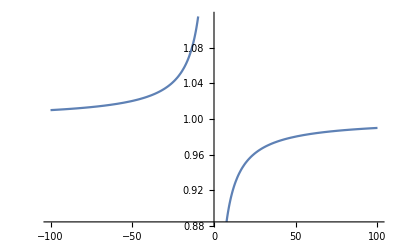

```mathematica
Plot[T[n], {n, -100, 100}]
```

```mathematica
fxn[n_] = n / ( n  +1 )
```

n/(1+n)

```mathematica
OddQ[Range[10]]
```

{True,False,True,False,True,False,True,False,True,False}

```mathematica
Event[Range[10]]
```

Event[{1,2,3,4,5,6,7,8,9,10}]

```mathematica
Alphabetic
```

AlphabeticOrder

```mathematica
correctQ[x_] := If[ x^2 < 25 , x, False]
```

```mathematica
correctQ[10]
```

False

```mathematica
Table[correctQ[x], {x, 1, 10}]
```

{1,2,3,4,False,False,False,False,False,False}

```mathematica
PrimeQ[10]
```

False

```mathematica
PrimeQ[Range[10]]
```

{False,True,True,False,True,False,True,False,False,False}

```mathematica
Divisors[60]
```

```mathematica
{1,2,3,4,5,6,10,12,15,20,30,60} // PrimeQ //Length
```

12

```mathematica
Subscript[fxn, 1][x_] :=
```

```mathematica
MemberQ[{1,2,3}, Null]
```

False

```mathematica
MemberQ[{1,2,3}, {}]
```

False

```mathematica
Count
```

Count[{1,2,3,4}]

```mathematica
MemberQ[{}, Null]
```

False

```mathematica
1 ==1
```

True

```mathematica
Null == {}
```

Null=={}

```mathematica
Primes
```

Primes

```mathematica
Solve [ x^2 - 25 == 0]
```

```mathematica
{{x->-5},{x->5}}[[1]][[1]] // Head
```

Rule

```mathematica
EvenQ[{1,2,3}]
```

{False,True,False}

```mathematica
Unique[{1,2,3}]
```

Unique::usym: 1 is not a symbol or a valid symbol name.

Unique[{1,2,3}]

```mathematica
even = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
odd = Range[11,20]
```

{11,12,13,14,15,16,17,18,19,20}

```mathematica
odd ∩ even
```

{}

```mathematica
( odd ∪ even ) - odd
```

Thread::tdlen: Objects of unequal length in {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}+{-11,-12,-13,-14,-15,-16,-17,-18,-19,-20} cannot be combined.

{-11,-12,-13,-14,-15,-16,-17,-18,-19,-20}+{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
{1,1,1} - {1,0}
```

Thread::tdlen: Objects of unequal length in {1,1,1}+{-1,0} cannot be combined.

{-1,0}+{1,1,1}

```mathematica
Union[even, odd]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
{1,2,3} * 2
```

{2,4,6}

```mathematica
{1,2,3} * {2,3}
```

Thread::tdlen: Objects of unequal length in {1,2,3} {2,3} cannot be combined.

{2,3} {1,2,3}

```mathematica
Tuples[{{2,4,6}, {1,2}}]
```

{{2,1},{2,2},{4,1},{4,2},{6,1},{6,2}}

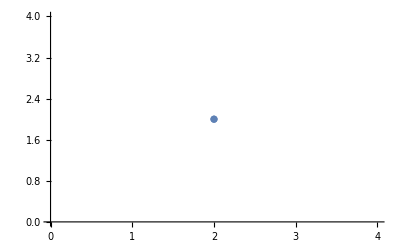

```mathematica
ListPlot[{{2,2}}]
```

```mathematica
Tuples[{{a,b,c}, {1,2}}]
```

{{a,1},{a,2},{b,1},{b,2},{c,1},{c,2}}